# 1D linear stability analysis (LSA) phase diagrams for the skeleton and switch models

Parameters transformed to the 1+1D geometry by bulk-boundary ratio of a cylinder of radius 0.5μm

```mathematica
paramsSwitch={
rhoD->varied,
rhoE->varied,
DD->16,
DE->10,
Dd->0.05,
Dde->0.05,
kD->1*4,
kdD->0.005*4,
kdEr->1.5*4,
kdEl->10^-5*2*4,
kde->1,
λ->5,
μ->20
};
```

## Setup

Setup the reaction terms for the 1+1D switch model

```mathematica
f={-λ cDD+kde mde,
λ cDD-(kD+kdD md)cDT,
-μ cEr+kde mde-kdEr md cEr,
μ cEr-kdEl md cEl,
(kD+kdD md)cDT-kdEr md cEr-kdEl md cEl,
kdEr md cEr+kdEl md cEl-kde mde
};
```

Conservation laws:

```mathematica
Simplify@Total@f[[{1,2,5,6}]]
Simplify[Total@f[[{3,4,6}]]]
```

0

0

## Homogeneous fixed point(s)

```mathematica
ClearAll@hss;
hss[params_]:=Block[{sol},
sol=NSolve[{0==f,rhoD==cDD+cDT+md+mde,rhoE==cEr+cEl+mde}/.params,{cDD,cDT,cEr,cEl,md,mde}];
Select[{cDD,cDT,cEr,cEl,md,mde}/.sol,AllTrue[#,NonNegative]&]
];
```

## LSA

```mathematica
eqs={-DD q^2cDD,
-DD q^2cDT,
-DE q^2cEr,
-DE q^2 cEl ,
-Dd q^2 md,
-Dde q^2 mde}+f;
```

```mathematica
jac=D[eqs,{{cDD,cDT,cEr,cEl,md,mde}}];
```

```mathematica
ClearAll@dispersionRelation;
Options[dispersionRelation]={"gpts"->100,"maxQ"->5};
dispersionRelation[params_,opts:OptionsPattern[]]:=Block[{gpts=OptionValue["gpts"],Q=OptionValue["maxQ"],HSS=hss[params],JAC},
JAC=(jac/.Thread[{cDD,cDT,cEr,cEl,md,mde}->#]/.params)&/@HSS;
{
Function[jj,{#,SortBy[Eigenvalues[jj/.q->#],Re[#]&]}&/@(Q Range[0,1,1/gpts])]/@JAC,
HSS
}
];
```

### Type-of-instability test

```mathematica
ClearAll@testInstab;
Options[testInstab]={"gpts"->100,"maxQ"->5};
testInstab[params_?(AllTrue[#,Function[x,NonNegative[x[[2]]]]]&),opts:OptionsPattern[]]:=Block[{
dispRel=dispersionRelation[params,"gpts"->OptionValue["gpts"],"maxQ"->OptionValue["maxQ"]],
HSS,
hssInd,
hssTypes,
hssLS,
sigma0,
qNZero,sigmaNZero,
sigmac,qc,
zero (*test whether there the dispersion relation is below 0 at q<qc*)
},
(*find laterally-unstable HSS*)
If[Length[dispRel[[1]]]==1,

HSS=dispRel[[2,1]];
dispRel=dispRel[[1,1]];
hssTypes=1;,(*just one steady state*)

(*locally stable hss*)
hssLS=Select[Range[Length[dispRel[[1]]]],Re[dispRel[[1,#,1,2,-1]]]< 10^-10&];

(*classify the hss's*)
If[Length[dispRel[[1]]]==2,
If[Length[hssLS]==0,
hssTypes=4;,(*two hss, both locally unstable*)
If[Length[hssLS]==1,
hssTypes=2;,(*two hss, one locally stable*)
hssTypes=3;];(*two hss, both locally stable*)
];,
If[Length[dispRel[[1]]]==3,
hssTypes=5;,(*three hss*)
hssTypes=6;];(*more than three hss*)
];

(*select the Turing-unstable hss, otherwise the most unstable hss*)
If[Length[hssLS]>0,
hssInd=Last@SortBy[hssLS,Max@Re[dispRel[[1,#,All,2,-1]]]&];
If[Max@Re[dispRel[[1,hssInd,All,2,-1]]]>0,
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];,
hssInd=Last@SortBy[Range[Length[dispRel[[1]]]],Max@Re[dispRel[[1,#,All,2,-1]]]&];
HSS=dispRel[[2,hssInd]];
dispRel=dispRel[[1,hssInd]];
];

];


sigma0=dispRel[[1,2,-1]];
qNZero=Min[Select[dispRel[[2;;]],Re@#[[2,-1]]<0&][[All,1]]];
If[qNZero==Infinity,
sigmaNZero=-1;,
sigmaNZero=SortBy[Select[dispRel,#[[1]]≥qNZero&],Re@#[[2,-1]]&][[-1,2,-1]];
];
{qc,sigmac}={#[[1]],#[[2,-1]]}&@First@Select[dispRel,Max[Re@dispRel[[All,2,-1]]]==Re@#[[2,-1]]&];
zero=If[qNZero<qc,1,0];
{
If[Re[sigma0]>10^-8,
If[qc==0,
If[Re@sigmaNZero>0,
2,(*type-III + type-I instability with sigma<0 in between*)
1],(*type-III instability*)
If[1==zero,
4,(*type-I + type-III instability with sigma<0 in between*)
3](*type-I + type-III instability with sigma>0 in between*)
],
If[qc==0,
0,(*no instability*)
If[1==zero,
5,(*type-I instability*)
6 ](*type-II instability*)
]
],
dispRel,
hssTypes,
HSS
}
];
```

## Variation in latent and reactive MinE concentrations

### LSA

```mathematica
Monitor[sweepLSASwitchLinear=Table[
{
rho,
testInstab[Join[{rhoD->3000/4,rhoE->rho/4},DeleteCases[paramsSwitch,(rhoD->_)|(rhoE->_)]]]
},{rho,10^Range[2,4.5,0.01]}];,rho]
```

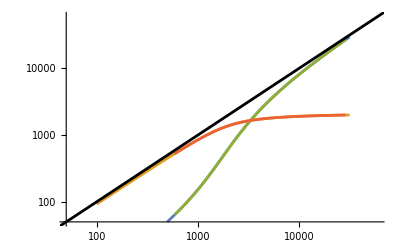

```mathematica
Show[
ListLogLogPlot[{
{#[[1]],4#[[2,-1,4]]}&/@sweepLSASwitchLinear,
{#[[1]],4#[[2,-1,3]]+4#[[2,-1,6]]}&/@sweepLSASwitchLinear,
{#[[1]],4#[[2,-1,4]]}&/@Select[sweepLSASwitchLinear,#[[2,1]]>0&],
{#[[1]],4#[[2,-1,3]]+4#[[2,-1,6]]}&/@Select[sweepLSASwitchLinear,#[[2,1]]>0&]
},Joined->True,PlotRange->{{50,60000},{50,60000}}],
LogLogPlot[x,{x,10,10^5},PlotStyle->Black]
]
```

### Time-averaged MinE concentrations in numerical simulations

The mde, cEr, and cEl densities where integrated over the surface and volume of the spherocylinder using Comsol Multiphysics, respectively. The integrated protein numbers where then divided by the volume of the spherocylinder. We average the concentrations at 2 s timesteps between 2000 s and 3000 s in the following.
Generate data with the Comsol setup file “switchModel-spherocylinder2DRotSymm-rhoD-3000-wavelength-period-MinEAvgConc-Sweep.mph”.
The averaging is found under the “Derived Values” header in the “Results” section.

#### mde

```mathematica
data=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-kD-1-kdD-0_005-kdEl-times2-rhoD-3000-rhoE-sweep-mdeAvg.txt","List"];
```

```mathematica
mdeLow=Partition[ToExpression/@StringSplit/@data[[6;;]],501];
```

```mathematica
data2=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-kD-1-kdD-0_005-kdEl-times2-rhoD-3000-rhoE-sweep-mdeAvg-highRhoE.txt","List"];
```

```mathematica
mdeTot=Join[mdeLow,Partition[ToExpression/@StringSplit/@data2[[6;;]],501]];
```

```mathematica
Dimensions@mdeTot
```

{9,501,3}

#### cEr and cEl

```mathematica
data=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-kD-1-kdD-0_005-kdEl-times2-rhoD-3000-rhoE-sweep-cEr-cEl-Avg.txt","List"];
```

```mathematica
cLow=Partition[ToExpression/@StringSplit/@data[[6;;]],501];
```

```mathematica
data2=Import[NotebookDirectory[]<>"switchModel-spherocylinder2DRotSymm-kD-1-kdD-0_005-kdEl-times2-rhoD-3000-rhoE-sweep-cEr-cEl-Avg-highRhoE.txt","List"];
```

```mathematica
cTot=Join[cLow,Partition[ToExpression/@StringSplit/@data2[[6;;]],501]];
```

```mathematica
Dimensions@cTot
```

{9,501,4}

#### combined

```mathematica
densities=Map[Flatten,Transpose[{cTot[[All,All,3;;]],mdeTot[[All,All,3;;]]},{3,1,2}],{2}];
```

```mathematica
timeAvgs={#[[1]],Mean[#[[2,All,2]]],Mean[#[[2,All,1]]+#[[2,All,3]]]}&/@Transpose[{cTot[[All,1,1]],densities}]
```

{{251.189,19.7436,231.423},{398.107,35.1818,362.89},{630.957,96.6265,534.272},{1000,297.76,702.153},{1584.89,673.321,911.435},{2511.89,1389.55,1122.12},{3981.07,2654.16,1326.57},{6309.57,4778.09,1530.95},{10000,8282.78,1716.36}}

### Result

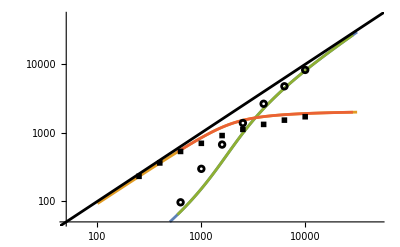

```mathematica
Show[
ListLogLogPlot[{
{#[[1]],4#[[2,-1,4]]}&/@sweepLSASwitchLinear,
{#[[1]],4#[[2,-1,3]]+4#[[2,-1,6]]}&/@sweepLSASwitchLinear,
{#[[1]],4#[[2,-1,4]]}&/@Select[sweepLSASwitchLinear,#[[2,1]]>0&],
{#[[1]],4#[[2,-1,3]]+4#[[2,-1,6]]}&/@Select[sweepLSASwitchLinear,#[[2,1]]>0&]
},Joined->True,PlotRange->{{50,50000},{50,50000}}],
LogLogPlot[x,{x,10,10^5},PlotStyle->Black],
ListLogLogPlot[{timeAvgs[[All,{1,2}]],
timeAvgs[[All,{1,3}]]},
PlotMarkers->{{Graphics[{Black,Circle[]}],0.04},{Graphics[{Black,Rectangle[]}],0.04}}]
]
```